# Print direction dependence

Used for “Printing direction dependent microstructure in direct ink writing”
Last updated November 2019 by Leanne Friedrich

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
<<"Mathematica\\orientation.wl";
bigtable2 = Import["Tables\\bigtable2_fulledge.csv"];
orients = Import["Tables\\orientation v2.csv"];
```

ErrorBar::shdw: Symbol ErrorBar appears in multiple contexts {ErrorBarPlots`,Global`}; definitions in context ErrorBarPlots` may shadow or be shadowed by other definitions.

# Theory

### motor error

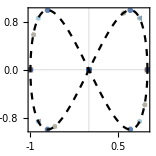
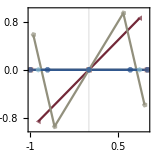
# of sides-Graphics-3 -Graphics-4 -Graphics-5 -Graphics-6 -Graphics-8 
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-

```mathematica
mtitle =  s8m[Column[{Row[{Subscript["v", "Tm"]}], OverBar[Row[{"v(", Subscript["c", "y"],"-",Subscript["c","x"],")"}]]}, Alignment->Center]];
figm = Column[{
rowprismlegend
,Row[theogridraw[cxcomponent, {-1,1}, 0, -1,0,False,mtitle]]
,Row[theogrid[cxcomponent, {-1,1}, 0, -1,0,True,mtitle]]
}, Alignment->Right]
```

```mathematica
Export["Figures\\basismotor.pdf", figm];
```

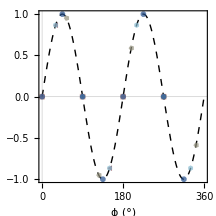
# of sides-Graphics-3 -Graphics-4 -Graphics-5 -Graphics-6 -Graphics-8 
-Graphics-

```mathematica
phiM = Column[{rowprismlegend, theophiplot[cxcomponent,mtitle,360,{-1,1},True]}, Alignment->Right]
```

```mathematica
Export["Figures\\phiM.pdf", phiM];
```

#### origin miscalibration

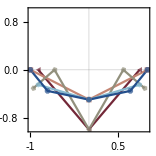
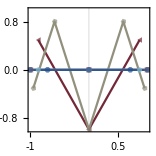
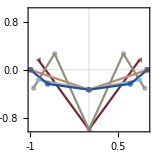
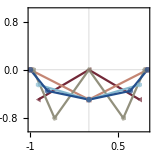
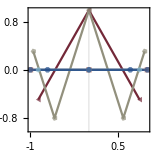
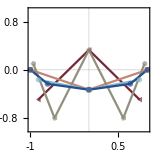
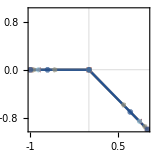
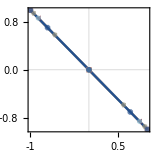
Line 1, -dx	
-Graphics--Graphics--Graphics-
Line 3, -dx	
-Graphics--Graphics--Graphics-
All lines, -dx	
-Graphics--Graphics--Graphics-Line 1, +dx	  # of sides-Graphics-3 -Graphics-4 -Graphics-5 -Graphics-6 -Graphics-8 
-Graphics--Graphics--Graphics-
Line 3, +dx	
-Graphics--Graphics--Graphics-
All lines, +dx	
-Graphics--Graphics--Graphics- | Line 1, -dy	
-Graphics--Graphics--Graphics-
Line 3, -dy	
-Graphics--Graphics--Graphics-
All lines, -dy	
-Graphics--Graphics--Graphics-Line 1, +dy	  # of sides-Graphics-3 -Graphics-4 -Graphics-5 -Graphics-6 -Graphics-8 
-Graphics--Graphics--Graphics-
Line 3, +dy	
-Graphics--Graphics--Graphics-
All lines, +dy	
-Graphics--Graphics--Graphics-
Line 1, -dx	
-Graphics--Graphics--Graphics-
Line 3, -dx	
-Graphics--Graphics--Graphics-
All lines, -dx	
-Graphics--Graphics--Graphics-Line 1, +dx	  # of sides-Graphics-3 -Graphics-4 -Graphics-5 -Graphics-6 -Graphics-8 
-Graphics--Graphics--Graphics-
Line 3, +dx	
-Graphics--Graphics--Graphics-
All lines, +dx	
-Graphics--Graphics--Graphics- | Line 1, -dy	
-Graphics--Graphics--Graphics-
Line 3, -dy	
-Graphics--Graphics--Graphics-
All lines, -dy	
-Graphics--Graphics--Graphics-Line 1, +dy	  # of sides-Graphics-3 -Graphics-4 -Graphics-5 -Graphics-6 -Graphics-8 
-Graphics--Graphics--Graphics-
Line 3, +dy	
-Graphics--Graphics--Graphics-
All lines, +dy	
-Graphics--Graphics--Graphics-

```mathematica
oxtitle =  s8m[Column[{Row[{Subscript["v", "To"], Subscript["τ", "o"]}], OverBar["|dx|"]}, Alignment->Center]];
oytitle =  s8m[Column[{Row[{Subscript["v", "To"], Subscript["τ", "o"]}], OverBar["|dy|"]}, Alignment->Center]];
figo = Table[
{Row[Table[
Column[Table[
Column[
{Row[{s8[Switch[linemode,{1},"Line 1",{ 3}, "Line 3", {1,2,3}, "All lines"]],", ",s8m[If[dx>0,"+","-"]<>"dx"], "\t", If[dx==1 && Length[linemode]==1&& linemode=={1}, rowprismlegend, ""]}]
,Row[f[vxdx[#, linemode, dx]&, {-1,1}, 0, -1,0,linemode=={1,2,3},oxtitle]]
}, Alignment->Left]
, {linemode,{{1}, {3},  {1,2,3}}}]]
, {dx, {-1,1}}]]
,Row[Table[
Column[Table[
Column[
{Row[{s8[Switch[linemode,{1},"Line 1",{ 3}, "Line 3", {1,2,3}, "All lines"]],", ",s8m[If[dx>0,"+","-"]<>"dy"], "\t", If[dx==1 && Length[linemode]==1&& linemode=={1}, rowprismlegend, ""]}]
,Row[f[vxdy[#, linemode, dx]&, {-1,1}, 0, -1,0,linemode=={1,2,3},oytitle]]
}, Alignment->Left]
, {linemode,{{1}, {3},  {1,2,3}}}]]
, {dx, {-1,1}}]]
}, {f, {theogrid, theogridraw}}];
Grid[figo]
```

```mathematica
Export["Figures\\basisox.pdf", Column[figo[[;;,1]]]];
Export["Figures\\basisoy.pdf", Column[figo[[;;,2]]]];
```

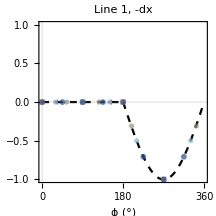
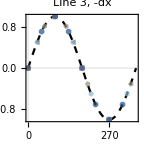
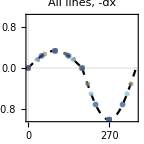
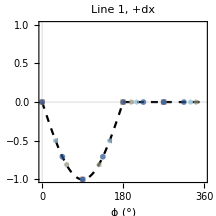
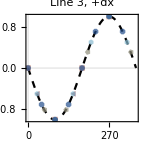
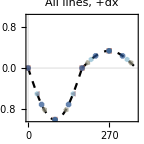
# of sides-Graphics-3 -Graphics-4 -Graphics-5 -Graphics-6 -Graphics-8 
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-

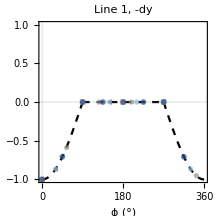
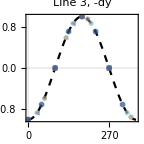
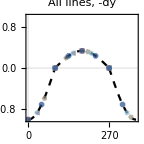
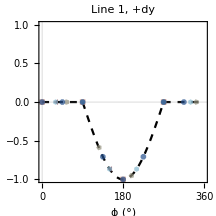
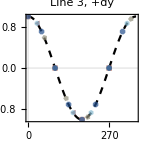
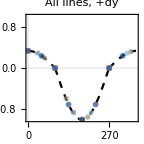
# of sides-Graphics-3 -Graphics-4 -Graphics-5 -Graphics-6 -Graphics-8 
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-

```mathematica
phiOx = Column[Join[{rowprismlegend}, Table[Row[
Table[
tg = Show[theophiplot[vxdx[#, linemode, dx]&,dtitle,360,{-1,1},linemode=={1}], PlotLabel->Row[{s8[Switch[linemode,{1},"Line 1",{ 3}, "Line 3", {1,2,3}, "All lines"]],", ",s8m[If[dx>0,"+","-"]<>"dx"]}]]
, {linemode,{{1}, {3},  {1,2,3}}}]], {dx, {-1, 1}}]], Alignment->Right]
phiOy = Column[Join[{rowprismlegend}, Table[Row[
Table[
tg = Show[theophiplot[vxdy[#, linemode, dx]&,dtitle,360,{-1,1},linemode=={1}], PlotLabel->Row[{s8[Switch[linemode,{1},"Line 1",{ 3}, "Line 3", {1,2,3}, "All lines"]],", ",s8m[If[dx>0,"+","-"]<>"dy"]}]]
, {linemode,{{1}, {3},  {1,2,3}}}]], {dx, {-1, 1}}]], Alignment->Right]
```

```mathematica
Export["Figures\\phiox.pdf", phiOx];
Export["Figures\\phioy.pdf", phiOy];
```

#### disturbed zone

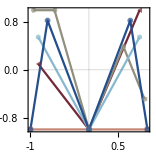
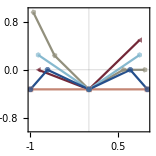
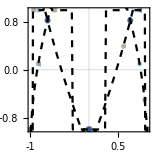
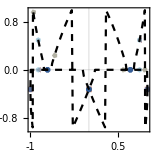
Middle	  # of sides-Graphics-3 -Graphics-4 -Graphics-5 -Graphics-6 -Graphics-8 
-Graphics--Graphics--Graphics-
Sides	
-Graphics--Graphics--Graphics-Middle	  # of sides-Graphics-3 -Graphics-4 -Graphics-5 -Graphics-6 -Graphics-8 
-Graphics--Graphics--Graphics-
Sides	
-Graphics--Graphics--Graphics-

```mathematica
dtitle =  s8m[Column[{Row[{Subscript["v", "Td"], "A"}], OverBar[Row[{Subscript["v", "d"], "wr"}]]}, Alignment->Center]];
figd = Row[Table[Column[Table[
Column[
{Row[{s8[Switch[var,I0[[1]],"Middle",IL[[1]], "Sides"]], "\t", If[var==I0[[1]], rowprismlegend, ""]}]
,Row[f[slidingx3[#, var]&, {-1,1}, 0, -1,0,var==IL[[1]],dtitle]]
}, Alignment->Left]
, {var, {I0[[1]], IL[[1]]}}]], {f, {theogrid, theogridraw}}]]
```

```mathematica
Export["Figures\\basisD.pdf", figd];
```

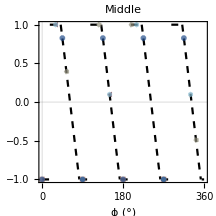
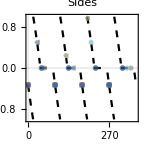
# of sides-Graphics-3 -Graphics-4 -Graphics-5 -Graphics-6 -Graphics-8 
-Graphics--Graphics-

```mathematica
phiD = Column[{rowprismlegend, Row[
Table[
tg = Show[theophiplot[slidingx3[#, var]&,dtitle,360,{-1,1}, var==I0[[1]]], PlotLabel->s8[Switch[var,I0[[1]],"Middle",IL[[1]], "Sides"]]]
,{var,  {I0[[1]], IL[[1]]}}]]}, Alignment->Right]
```

```mathematica
Export["Figures\\phiD.pdf", phiD];
```

#### solid rotation

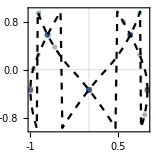
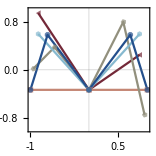
# of sides-Graphics-3 -Graphics-4 -Graphics-5 -Graphics-6 -Graphics-8 
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-

```mathematica
stitle =  s8m[Column[{Row[{Subscript["v", "Ts"], Subscript["τ", "s"]}], OverBar["w"]}, Alignment->Center]];
figs = Column[
{ rowprismlegend
,Row[theogridraw[rigidmodel, {-1,1}, 0, -1,0,False,stitle]]
,Row[theogrid[rigidmodel, {-1,1}, 0, -1,0,True,stitle]]
}, Alignment->Right]
```

```mathematica
Export["Figures\\basisS.pdf", figs];
```

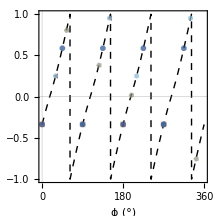
# of sides-Graphics-3 -Graphics-4 -Graphics-5 -Graphics-6 -Graphics-8 
-Graphics-

```mathematica
phiS = Column[{rowprismlegend, theophiplot[rigidmodel,stitle,360,{-1,1},True]}, Alignment->Right]
```

```mathematica
Export["Figures\\phiS.pdf", phiS];
```

#### Fluid reshaping

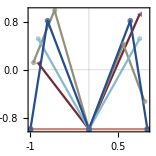
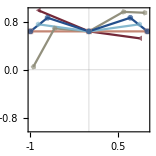
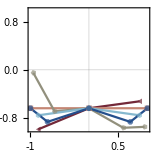
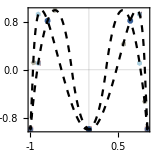
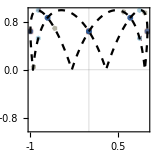
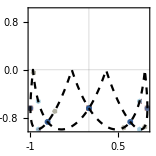
Middle	  # of sides-Graphics-3 -Graphics-4 -Graphics-5 -Graphics-6 -Graphics-8 
-Graphics--Graphics--Graphics-
Outer	
-Graphics--Graphics--Graphics-
Inner	
-Graphics--Graphics--Graphics-Middle	  # of sides-Graphics-3 -Graphics-4 -Graphics-5 -Graphics-6 -Graphics-8 
-Graphics--Graphics--Graphics-
Outer	
-Graphics--Graphics--Graphics-
Inner	
-Graphics--Graphics--Graphics-

```mathematica
rtitle =  s8m[Column[{Row[{Subscript["v", "Tr"], "A"}], OverBar[Row[{Subscript["v", "e"], Superscript["w", "2"]}]]}, Alignment->Center]];
figr = Row[Table[Column[Table[
Column[
{Row[{s8[Switch[var,I0[[1]],"Middle",IL[[1]], "Outer", IR[[1]], "Inner"]], "\t", If[var==I0[[1]], rowprismlegend, ""]}]
,Row[f[faststa[#, var]&, {-1,1}, 0, -1,0,var==IR[[1]],rtitle]]
}, Alignment->Left]
, {var, {I0[[1]], IL[[1]], IR[[1]]}}]], {f, {theogrid, theogridraw}}]]
```

```mathematica
Export["Figures\\basisR.pdf", figr];
```

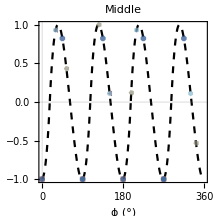
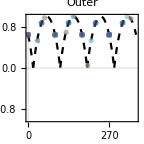
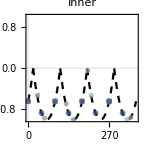
# of sides-Graphics-3 -Graphics-4 -Graphics-5 -Graphics-6 -Graphics-8 
-Graphics--Graphics--Graphics-

```mathematica
phiR = Column[{rowprismlegend, Row[
Table[
tg = Show[theophiplot[faststa[#, var]&,rtitle,360,{-1,1}, var==I0[[1]]], PlotLabel->s8[Switch[var,I0[[1]],"Middle",IL[[1]], "Outer", IR[[1]], "Inner"]]]
,{var,  {I0[[1]], IL[[1]], IR[[1]]}}]]}, Alignment->Right]
```

```mathematica
Export["Figures\\phiR.pdf", phiR];
```

## Fit experimental profiles

### graphical examples

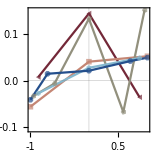
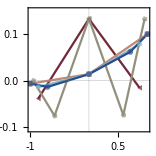
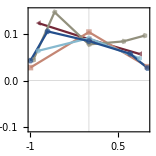
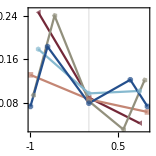
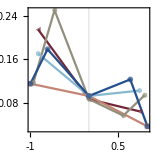
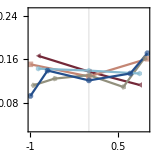
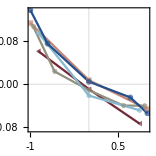
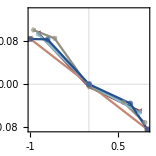
nozzle
Layer-by-layer
  # of sides-Graphics-3 -Graphics-4 -Graphics-5 -Graphics-6 -Graphics-8 -Graphics-
Experimental | -Graphics- | -Graphics- | -Graphics-
Fitted | -Graphics- | -Graphics- | -Graphics-
Corrected | -Graphics- | -Graphics- | -Graphics-    ahead
Layer-by-layer
  # of sides-Graphics-3 -Graphics-4 -Graphics-5 -Graphics-6 -Graphics-8 -Graphics-
Experimental | -Graphics- | -Graphics- | -Graphics-
Fitted | -Graphics- | -Graphics- | -Graphics-
Corrected | -Graphics- | -Graphics- | -Graphics-    Line 3
Layer-by-layer
  # of sides-Graphics-3 -Graphics-4 -Graphics-5 -Graphics-6 -Graphics-8 -Graphics-
Experimental | -Graphics- | -Graphics- | -Graphics-
Fitted | -Graphics- | -Graphics- | -Graphics-
Corrected | -Graphics- | -Graphics- | -Graphics-    Line 2
Layer-by-layer
  # of sides-Graphics-3 -Graphics-4 -Graphics-5 -Graphics-6 -Graphics-8 -Graphics-
Experimental | -Graphics- | -Graphics- | -Graphics-
Fitted | -Graphics- | -Graphics- | -Graphics-
Corrected | -Graphics- | -Graphics- | -Graphics-    Line 1
Layer-by-layer
  # of sides-Graphics-3 -Graphics-4 -Graphics-5 -Graphics-6 -Graphics-8 -Graphics-
Experimental | -Graphics- | -Graphics- | -Graphics-
Fitted | -Graphics- | -Graphics- | -Graphics-
Corrected | -Graphics- | -Graphics- | -Graphics-

11 | 2 | 0 | 0 | -0.177186 | 0.0793923 | -0.034636 | 0.00570504 | 0.0777338 | 0.00465249 | -0.000889473 | 0.0124759 | 0.0785309 | 0.00455574 | 0.00160633 | 0.00567445 | 0.0779709 | 0.00461421 | -0.000919347 | 2 | 0.0124759 | 0.0785309 | 0.00455574 | 0.00160633 | 0.0769246
13 | 2 | 0 | 0 | 0.00880326 | -0.0583834 | -0.0654785 | 0.0384042 | 0.127112 | 0.00266743 | -0.00598759 | 0.0707435 | 0.131598 | 0.00333362 | 0.00910857 | 0.0388049 | 0.128737 | 0.00225809 | -0.00628697 | 3 | 0.0388049 | 0.128737 | 0.00225809 | -0.00628697 | 0.135024
31 | 2 | 0 | 0 | 0.00484215 | -0.0843982 | -0.00633109 | 0.0130298 | 0.0109278 | 0.00365539 | -0.00203147 | 0.0216822 | 0.0122956 | 0.00382944 | 0.00279169 | 0.013272 | 0.0114842 | 0.00370796 | -0.00215027 | 1 | 0.0130298 | 0.0109278 | 0.00365539 | -0.00203147 | 0.0129593
37 | 2 | 0 | 0 | 0.0113921 | -0.0748521 | -0.00255803 | 0.011839 | 0.0265871 | 0.00405275 | -0.00184582 | 0.0194564 | 0.0278136 | 0.00421995 | 0.00250511 | 0.0120703 | 0.0270932 | 0.00409752 | -0.00195557 | 1 | 0.011839 | 0.0265871 | 0.00405275 | -0.00184582 | 0.0284329
43 | 2 | 0 | 0 | 0.00352075 | -0.075234 | -0.00764678 | 0.00956284 | 0.0314071 | 0.00367425 | -0.00149094 | 0.0155497 | 0.0323869 | 0.00380559 | 0.0020021 | 0.00975728 | 0.0318163 | 0.00370424 | -0.00158083 | 1 | 0.00956284 | 0.0314071 | 0.00367425 | -0.00149094 | 0.0328981

```mathematica
dt = Table[detectbasis[bigtable2, i, 2, True, 0, 0], {i, {11, 13, 31, 37, 43}}];
Row[dt[[;;,1]]]
Grid[dt[[;;,2]]]
```

### go through all dependent variables and split by independent variable, export as table

```mathematica
If[!DirectoryQ["orienttables"], CreateDirectory["orienttables"]];
Do[
Do[
t1 = Flatten[Table[
detectbasis[bigtable2, i, mode,False, svar, t][[2]]
, {mode, 2, 3}, {i, Join[Range[11, 29, 2], {31, 37, 43}]}],1];
fn = "orienttables\\orientation_"<>ToString[svar]<>"_"<>ToString[t]<>"v2.csv";
Export[fn, Prepend[t1, ORIENTHEADER2]];
Print[fn];
, {t,If[svar>0,  DeleteDuplicates[bigtable2[[2;;, svar]]], {0}]}];
, {svar, {0, 1,2,4}}]
```

orienttables\orientation_0_0v2.csv

orienttables\orientation_1_20v2.csv

orienttables\orientation_1_25v2.csv

orienttables\orientation_1_30v2.csv

orienttables\orientation_1_35v2.csv

orienttables\orientation_2_12v2.csv

orienttables\orientation_2_3v2.csv

orienttables\orientation_2_6v2.csv

orienttables\orientation_2_9v2.csv

orienttables\orientation_4_6v2.csv

orienttables\orientation_4_8v2.csv

orienttables\orientation_4_10v2.csv

orienttables\orientation_4_12v2.csv

```mathematica
orients = Flatten[Import/@FileNames["*v2*", "orienttables", Infinity],1];
```

```mathematica
Export["Tables\\orientation v2.csv", DeleteDuplicates[orients]]
```

Tables\orientation v2.csv

## Fit quality

### Flow velocities

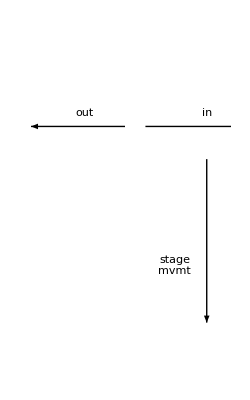
○ Layer-by-layer  ● Bath
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
DSRlegend
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
bf = Column[{plegend[Row], Row[Table[bfcatplot[orients, var, var==11, var==29, 10, 6.5], {var, 11, 29, 2}]]}, Alignment->Right];
dsr = Column[{DSRlegend
, Column[Table[
Row[Table[
DSRerrplot[orients, var, var==11, var==29, 10, 6.5, yi]
, {var, 11, 29, 2}]]
, {yi, {8, 10}}]
]}, Alignment->Right];
Column[Join[{bf, dsr}, Reverse[rlegends[{}, 50][[2;;]]]]]
```

```mathematica
Column[
Join[
{plegend[Row]}
,
Table[
Row[Table[
fitplot[orients, var, var==11, var==29, 10, 6.5, yindex]
, {var, 11, 29,2}]]
, {yindex, {13, 5, 6, 7, 12}}]
,
Reverse[rlegends[{}, 50][[2;;]]]
]
,Alignment->Right
]
```

○ Layer-by-layer  ● Bath
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

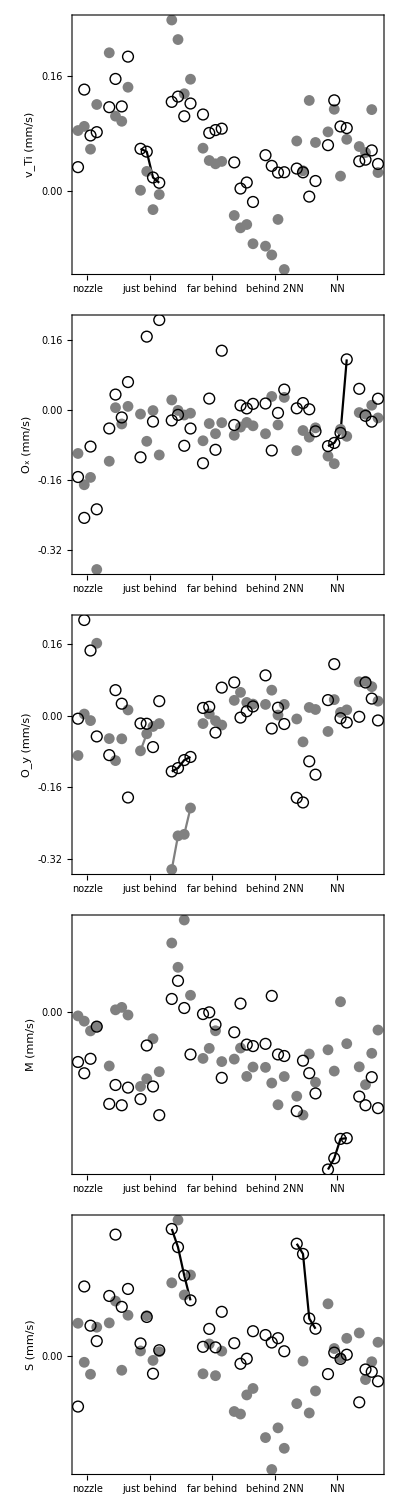
TEGDMA 20, 25, 30, 35%○ Layer-by-layer  ● Bath
-Graphics-

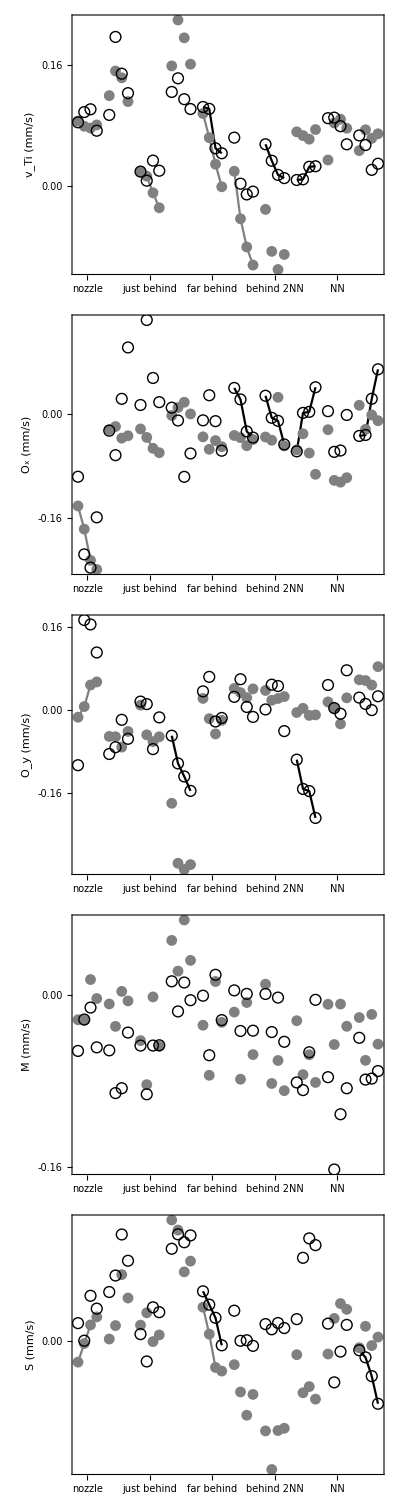
Print speed 3, 6, 9, 12 mm/s○ Layer-by-layer  ● Bath
-Graphics-

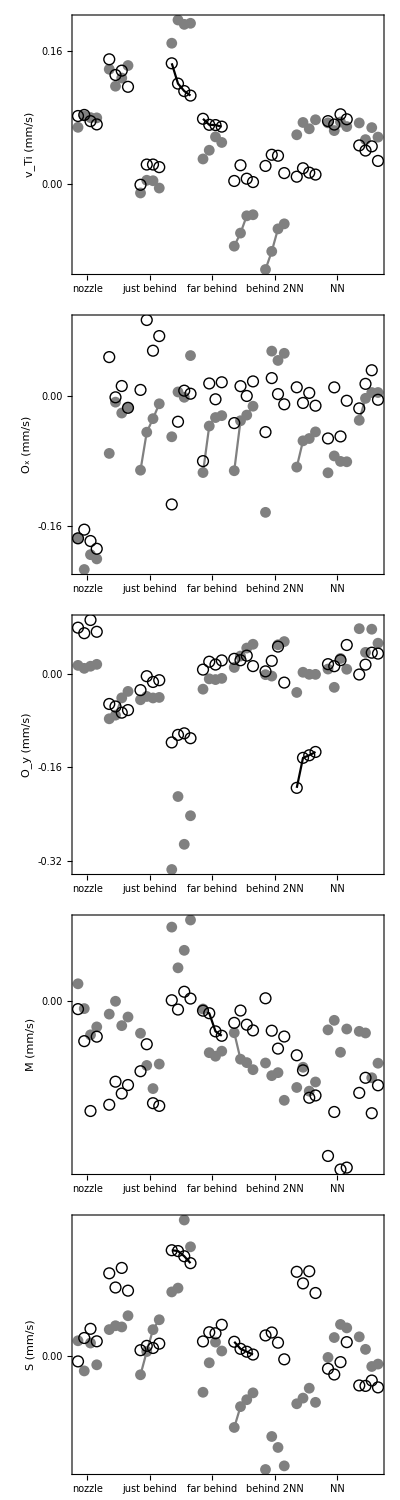
Edge length 6, 8, 10, 12 mm○ Layer-by-layer  ● Bath
-Graphics-

```mathematica
se1 = spliteffects[orients, 1]
Export["Figures\\orientsvtteg.pdf", se1];
se1 = spliteffects[orients, 2]
Export["Figures\\orientsvtv.pdf", se1];
se1 = spliteffects[orients, 4]
Export["Figures\\orientsvtedge.pdf", se1];
```

### Particle distribution positions

```mathematica
is = 2.25;
bf = Row[Table[
bfcatplot[orients, var, var==43, var==31,3,is]
, {var, {43, 37, 31}}]];
dsr = Column[Table[
Row[Table[
DSRerrplot[orients, var, var==43, var==31, 3,is, yi]
, {var, {43, 37, 31}}]]
, {yi, {8, 10}}]
];
Row[{Column[{bf, dsr, hllegend[is]}]," ", Column[{plegend[Column],"\t", DSRlegend[Column[Riffle[#, ConstantArray["\t",2]]]&]}]}]
```

-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics- ○ Layer-by-layer
  
● Bath
	
● Disturbed zone (D) 
	
■ Solid rotation (S) 
	
▲ Fluid reshaping (R)

```mathematica
Column[{
plegend[Row]
,
Row[{
Graphics[{Text[s8@"-0.15", {0, -0.15}], Text[s8@"0.00", {0, 0}], Text[s8@"0.15", {0,0.15}]}, ImageSize->30, PlotRange->{-0.2, 0.17}, AspectRatio->4.5]
,
Row[
Table[
Column[{
ylab[43, yindex], 
Row[Table[
Column[{fitplot[orients, var,1, var==31, 16, 6.5, yindex], s8[(49-var)/6]}, Alignment->Center]
, {var, {43, 37, 31}}]]
, s8@"Line"
}, Alignment->Center]
, {yindex, {13, 5, 6, 7, 12}}], " "]
}]
}, Alignment->Right]
```

○ Layer-by-layer  ● Bath
-Graphics-  L_i (mm/s)
-Graphics-
1-Graphics-
2-Graphics-
3
LineO_x (mm/s)
-Graphics-
1-Graphics-
2-Graphics-
3
LineO_y (mm/s)
-Graphics-
1-Graphics-
2-Graphics-
3
LineM (mm/s)
-Graphics-
1-Graphics-
2-Graphics-
3
LineS (mm/s)
-Graphics-
1-Graphics-
2-Graphics-
3
Line

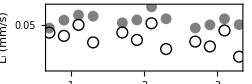
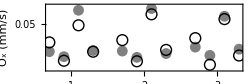
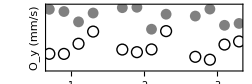
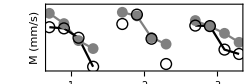
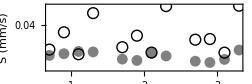
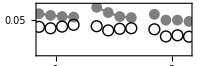
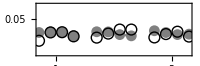
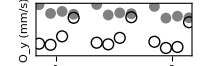
○ Layer-by-layer  ● Bath
TEGDMA 20, 25, 30, 35%
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-Print speed 3, 6, 9, 12 mm/s
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-Edge length 6, 8, 10, 12 mm
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
s2= Column[{plegend[Row], Row[Table[spliteffectspos[orients, i], {i, { 1, 2, 4}}], Alignment->Bottom]}, Alignment->Right]
```

```mathematica
Export["Figures\\orientsLparams.pdf", s2];
```

## Particle distribution widths

### Theory

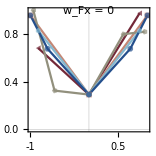
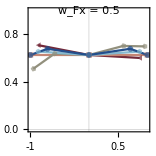
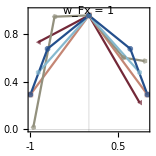
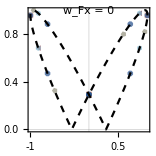
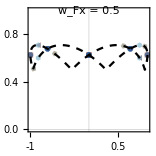
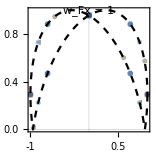
# of sides-Graphics-3 -Graphics-4 -Graphics-5 -Graphics-6 -Graphics-8 
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-  # of sides-Graphics-3 -Graphics-4 -Graphics-5 -Graphics-6 -Graphics-8 
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-

```mathematica
basisF = Row[Table[Column[{
rowprismlegend
,Column[Table[
tg = f[focusxy[#,wfx]&, {0,1}, 0, -1,0,wfx==1, s8m[Column[{Subscript["w", "Fa"], OverBar[Subscript["w", "p"]]}]]];
tg[[1]] = Show[tg[[1]],  Graphics[Text[Row[{s8m[Subscript["w", "Fx"]],s8[ " = "<>ToString[wfx]]}], {0, 1}, {Center, Center}]]];
Row[tg]
,{wfx, {0, 0.5, 1}}
]]
}, Alignment->Right], {f, {theogrid, theogridraw}}]]
```

```mathematica
Export["Figures\\basisF.pdf", basisF];
```

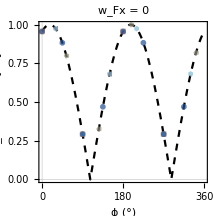
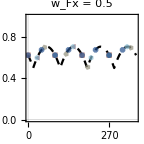
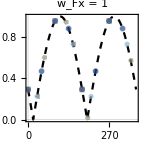

```mathematica
phiF = Row[
Table[
tg = Show[theophiplot[focusxy[#,wfx]&, s8m[Column[{Subscript["w", "Fa"], OverBar[Subscript["w", "p"]]}]],360,{0,1},wfx==0], PlotLabel->s8[Row[{s8m[Subscript["w", "Fx"]],s8[ " = "<>ToString[wfx]]}]]]
,{wfx, {0, 0.5, 1}}]]
```

```mathematica
Export["Figures\\phiF.pdf", phiF];
```

### Experiments

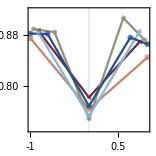
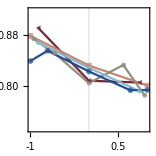
Layer-by-layer	  # of sides-Graphics-3 -Graphics-4 -Graphics-5 -Graphics-6 -Graphics-8 
-Graphics--Graphics--Graphics-
Bath	
-Graphics--Graphics--Graphics-

```mathematica
Column[Table[
Column[
{Row[{s8[Switch[mode,2, "Layer-by-layer", 3, "Bath"]],"\t", If[mode==2, rowprismlegend, ""]}]
,
wfplots[Select[bigtable2, #[[3]]==mode&], mode==3, {0.73, 0.92}]
}, Alignment->Left]
, {mode, 2,3}]]
```

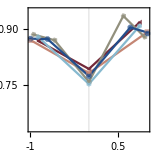
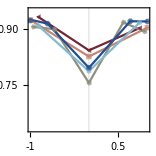
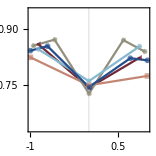
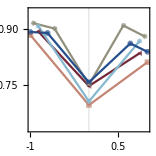
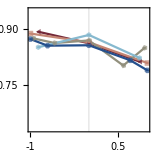
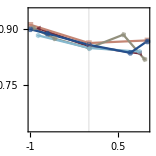
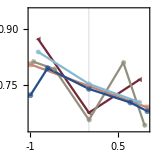
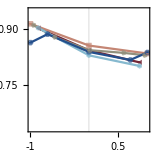
Layer-by-layer	
20 w% TEGDMA
-Graphics--Graphics--Graphics-
25 w% TEGDMA
-Graphics--Graphics--Graphics-
30 w% TEGDMA
-Graphics--Graphics--Graphics-
35 w% TEGDMA
-Graphics--Graphics--Graphics-Bath	  # of sides-Graphics-3 -Graphics-4 -Graphics-5 -Graphics-6 -Graphics-8 
20 w% TEGDMA
-Graphics--Graphics--Graphics-
25 w% TEGDMA
-Graphics--Graphics--Graphics-
30 w% TEGDMA
-Graphics--Graphics--Graphics-
35 w% TEGDMA
-Graphics--Graphics--Graphics-

```mathematica
wfplotgrid[bigtable2, 1, {0.63, 0.95}]
```

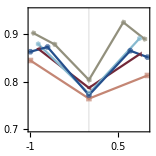
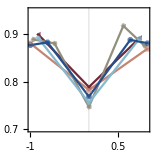
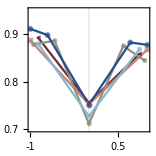
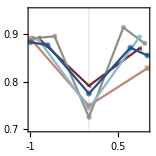
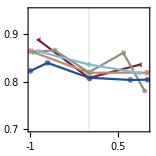
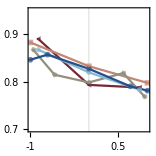
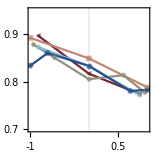
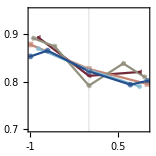
Layer-by-layer	
Print speed 3 (mm/s)
-Graphics--Graphics--Graphics-
Print speed 6 (mm/s)
-Graphics--Graphics--Graphics-
Print speed 9 (mm/s)
-Graphics--Graphics--Graphics-
Print speed 12 (mm/s)
-Graphics--Graphics--Graphics-Bath	  # of sides-Graphics-3 -Graphics-4 -Graphics-5 -Graphics-6 -Graphics-8 
Print speed 3 (mm/s)
-Graphics--Graphics--Graphics-
Print speed 6 (mm/s)
-Graphics--Graphics--Graphics-
Print speed 9 (mm/s)
-Graphics--Graphics--Graphics-
Print speed 12 (mm/s)
-Graphics--Graphics--Graphics-

```mathematica
wfplotgrid[bigtable2, 2, {0.7, 0.95}]
```

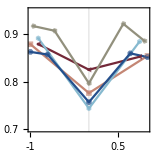
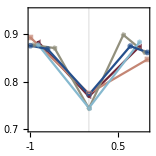
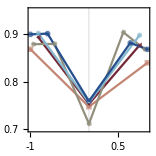
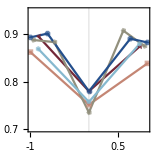
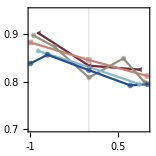
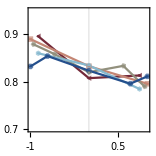
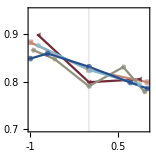
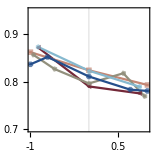
Layer-by-layer	
Edge length 6 (mm)
-Graphics--Graphics--Graphics-
Edge length 8 (mm)
-Graphics--Graphics--Graphics-
Edge length 10 (mm)
-Graphics--Graphics--Graphics-
Edge length 12 (mm)
-Graphics--Graphics--Graphics-Bath	  # of sides-Graphics-3 -Graphics-4 -Graphics-5 -Graphics-6 -Graphics-8 
Edge length 6 (mm)
-Graphics--Graphics--Graphics-
Edge length 8 (mm)
-Graphics--Graphics--Graphics-
Edge length 10 (mm)
-Graphics--Graphics--Graphics-
Edge length 12 (mm)
-Graphics--Graphics--Graphics-

```mathematica
wfplotgrid[bigtable2, 4, {0.7, 0.95}]
```